## Preamble

```mathematica
LaunchKernels[10];
<< KerrGeodesics`
<< GeneralRelativityTensors`
<<SpinWeightedSpheroidalHarmonics`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"];
ParallelNeeds["Teukolsky`"];
ParallelNeeds["KerrGeodesics`"];
Information[PacletObject["Teukolsky"]]
```

Paclet

## Calculating ϕ_1

## Calculating homogenous Φ_1 given a radius r

```mathematica
ϕ1[a_,p_,e_, l_,m_,n_]:=Module[{Ω,ω, Σ, Δ, Trad, Tradmino, orbit, t0,r0,θ0, ϕ0, Q0,K0,Β, λ, prec=32},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,1];
ω=m Ω[[3]] + n Ω[[1]];
Trad =2π/Ω[[1]];
Tradmino=2π/KerrGeoFrequencies[a,p,e,1,Time->"Mino"][[1]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],SetPrecision[1,prec]];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
Q0 := m-a ω[m,n];
K0[λ_]:= ω[m,n](r0[λ]^2 + a^2)- a m;
λ = SpinWeightedSpheroidalEigenvalue[1,l,m,a ω];
Β= Sqrt[λ^2+ 4 a m ω - 4 a^2 ω^2];
(*To Do: calculate g_(+1) and Subscript[f, -1] and then combine them to calculate Subscript[ϕ, 1]*)
]
```

## Calculating ϕ_0 and ϕ_2

```mathematica
OrbitTP[p_,e_]:= Module[{},{rMax, rMin}/.NSolve[{p== (2 rMax rMin)/(rMax + rMin), e == (rMax-rMin)/(rMax + rMin)}, {rMax, rMin}][[1]]
]
```

```mathematica
LMAX = 5;NMAX=2;
```

```mathematica
Φ0 [a_ , r_ ,τmino_, p_,e_,l_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
 Δ^-1 Total[Flatten[sum]]
]
```

```mathematica
Φ0New[a_ ,p_,e_,τmino_,  r_,l_]:=Module[{Ω,orbit,numberOfRs, t0,r0,θ0,ϕ0, rmax,rmin,outputlist, Δ, sum,M=1,prec=32},
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];

numberOfRs = Length[r];
If[numberOfRs==0, 
Δ=r^2-2 M r + a^2;
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
 Δ^-1 Total[Flatten[sum]],
(*If r is a list*)
outputlist=Table[0,{i,1,numberOfRs}];
Module[{m,n,R, ω,mode,α,S,P,i, expFactor},
m=-l;
While[m<=l,
n=-NMAX;
While[n<=NMAX,
ω= m Ω[[3]] + n Ω[[1]];
R= TeukolskyRadial[1,l,m,a, ω];
mode =TeukolskyPointParticleMode[1 , l,m,n,0,orbit];
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
i = 1;
While[i<=numberOfRs,
Δ=r[[i]]^2-2 M r[[i]] + a^2;
If[r[[i]]>=r0[τmino],
P=R["Up"][r[[i]]]Δ;
α=mode["Amplitudes"]["ℐ"];
outputlist[[i]]=outputlist[[i]]+Δ^-1 S expFactor α P,
P=R["In"][r[[i]]]Δ;
α=mode["Amplitudes"]["ℋ"];
outputlist[[i]]=outputlist[[i]]+Δ^-1 S expFactor α P,
];
i=i+1;
];
n=n+1;
];
m=m+1;
];
];
outputlist
]
]
```

```mathematica
AbsoluteTiming[Φ0New[0 ,10,0.1,0.5,  Subdivide[6,30,100],1]]
```

{17.4705,{2.71051×10^-20+0.00511616 ⅈ,1.6263×10^-19+0.00511154 ⅈ,-2.71051×10^-20+0.00510704 ⅈ,-5.42101×10^-20+0.00510261 ⅈ,-2.71051×10^-20+0.00509821 ⅈ,-2.71051×10^-20+0.00509381 ⅈ,-2.71051×10^-20+0.00508939 ⅈ,2.71051×10^-19+0.00508493 ⅈ,5.42101×10^-20+0.00508041 ⅈ,2.71051×10^-20+0.00507582 ⅈ,-5.42101×10^-20+0.00507115 ⅈ,8.13152×10^-20+0.00506638 ⅈ,0.+0.0050615 ⅈ,-5.42101×10^-20+0.00505652 ⅈ,-2.71051×10^-20+0.00505142 ⅈ,-8.13152×10^-20+0.0050462 ⅈ,3.05706×10^-15+0.00754194 ⅈ,-1.38522×10^-15+0.00691586 ⅈ,1.59596×10^-14+0.00635483 ⅈ,-2.37377×10^-15+0.00585067 ⅈ,-1.70536×10^-15+0.00539643 ⅈ,-1.23005×10^-15+0.00498614 ⅈ,-8.90128×10^-16+0.00461466 ⅈ,-6.49251×10^-16+0.00427756 ⅈ,-4.7237×10^-16+0.00397099 ⅈ,-8.6903×10^-16+0.00369163 ⅈ,1.7506×10^-16+0.00343655 ⅈ,-1.49974×10^-15+0.00320321 ⅈ,6.40713×10^-17+0.00298938 ⅈ,1.83666×10^-15+0.00279308 ⅈ,1.66274×10^-15+0.00261258 ⅈ,-6.92523×10^-16+0.00244635 ⅈ,-5.82963×10^-16+0.00229303 ⅈ,-2.88205×10^-16+0.00215142 ⅈ,9.3988×10^-17+0.00202043 ⅈ,2.75148×10^-16+0.00189911 ⅈ,-4.51803×10^-17+0.00178659 ⅈ,-3.37771×10^-17+0.00168212 ⅈ,-2.51416×10^-17+0.00158499 ⅈ,-1.81542×10^-17+0.0014946 ⅈ,-1.39896×10^-17+0.00141037 ⅈ,-1.04352×10^-17+0.0013318 ⅈ,-8.25857×10^-18+0.00125844 ⅈ,-6.30637×10^-18+0.00118988 ⅈ,-5.13556×10^-18+0.00112573 ⅈ,-3.87348×10^-18+0.00106566 ⅈ,-2.93645×10^-18+0.00100936 ⅈ,-2.63957×10^-18+0.000956536 ⅈ,-2.07396×10^-18+0.000906945 ⅈ,-2.1967×10^-17+0.000860345 ⅈ,-1.68019×10^-17+0.000816521 ⅈ,-1.24208×10^-17+0.000775278 ⅈ,-4.14696×10^-16+0.000736432 ⅈ,3.73831×10^-17+0.00069982 ⅈ,2.99036×10^-17+0.000665287 ⅈ,2.38002×10^-17+0.000632695 ⅈ,-1.36513×10^-16+0.000601912 ⅈ,3.10308×10^-18+0.000572822 ⅈ,1.98189×10^-18+0.000545312 ⅈ,1.35092×10^-18+0.000519282 ⅈ,6.67197×10^-19+0.000494638 ⅈ,2.53157×10^-19+0.000471292 ⅈ,1.69671×10^-19+0.000449164 ⅈ,-1.90212×10^-19+0.000428179 ⅈ,-3.07685×10^-19+0.000408268 ⅈ,-2.76133×10^-19+0.000389365 ⅈ,-1.4336×10^-19+0.000371412 ⅈ,-2.60569×10^-19+0.000354352 ⅈ,-3.00432×10^-19+0.000338133 ⅈ,-1.47595×10^-19+0.000322706 ⅈ,1.52347×10^-17+0.000308027 ⅈ,1.2827×10^-17+0.000294054 ⅈ,1.09725×10^-17+0.000280746 ⅈ,9.04832×10^-18+0.000268067 ⅈ,7.33298×10^-18+0.000255982 ⅈ,-1.56119×10^-19+0.000244459 ⅈ,-1.74806×10^-19+0.000233469 ⅈ,-4.70103×10^-20+0.000222981 ⅈ,-6.99861×10^-20+0.000212971 ⅈ,3.36696×10^-20+0.000203412 ⅈ,-5.03985×10^-20+0.000194282 ⅈ,4.7328×10^-20+0.000185559 ⅈ,8.80914×10^-20+0.00017722 ⅈ,1.31078×10^-19+0.000169249 ⅈ,1.33725×10^-19+0.000161624 ⅈ,2.21817×10^-19+0.000154331 ⅈ,-8.08916×10^-19+0.000147352 ⅈ,-6.46921×10^-19+0.000140671 ⅈ,-5.55124×10^-19+0.000134275 ⅈ,-3.93235×10^-19+0.000128149 ⅈ,-2.21287×10^-19+0.000122282 ⅈ,-2.16523×10^-19+0.000116659 ⅈ,-4.58996×10^-17+0.000111271 ⅈ,5.94056×10^-18+0.000106106 ⅈ,5.05192×10^-18+0.000101154 ⅈ,4.43877×10^-18+0.0000964043 ⅈ,3.71064×10^-18+0.0000918486 ⅈ,3.1769×10^-18+0.0000874779 ⅈ,2.72766×10^-18+0.0000832837 ⅈ,2.35168×10^-18+0.0000792584 ⅈ,2.05215×10^-18+0.0000753943 ⅈ}}

```mathematica
AbsoluteTiming[Φ0New[0 ,10,0.1,0.5, 50,1]]
```

{9.65723,9.95731×10^-18-0.0000163595 ⅈ}

```mathematica
Table[0,{i,1Length[{10,30}]}]
```

{0,0}

```mathematica
Φ2 [a_ , r_ ,τmino_, p_,e_,l_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
If[r<= r0[τmino],
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[-1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[-1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[-1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{m,-l,l},{n,-NMAX,NMAX}
];
];
1/(2(r-ⅈ a Cos[θ0[τmino]])^2)Δ^-1 Total[Flatten[sum]]
]
```

```mathematica
AbsoluteTiming[Φ0[0, 20 ,0.5, 10,0.1,1]]
```

{11.8167,1.65762×10^-18+0.000536476 ⅈ}

```mathematica
Module[{m},
m=-1;
While[m<=1,Print[m];m=m+1]
]
```

-1

0

1

## Plotting Φ_0

### Sum over l

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ0 = Monitor[Table[Φ0 [a , lowerRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],i];
upperΦ0 =Monitor[Table[Φ0 [a , upperRs[[i]] ,τmino, p,e,1],{i,1 ,Length[lowerRs]}],50+i];
]
```

$Aborted

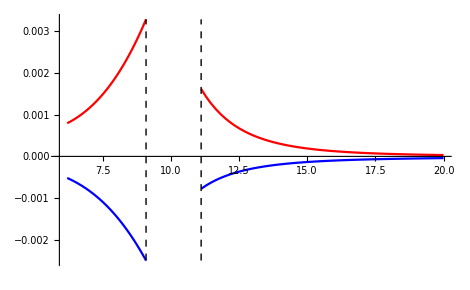

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ0],Im[lowerΦ0], Re[upperΦ0],Im[upperΦ0]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ0[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ0[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

### l = 1 mode

```mathematica
AbsoluteTiming[Module[{orbit,modes,rmin, rmax,t0,r0,θ0,ϕ0,τmino=0.5,numpts = 10,p=10,e=0.1,l=1,prec=32,a=0},
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
modes = Flatten[Table[Module[{},
TeukolskyPointParticleMode[-1,l, m,n,0,orbit]],{m,-l,l},{n,-NMAX,NMAX}]];
{rmax, rmin} = OrbitTP[p,e];
RH = Subdivide[KerrGeoSeparatrix[a,e,1],r0[τmino],numpts/2];
RI = Subdivide[r0[τmino], rmin+rmax,numpts/2];
modes[[1]]["ExtendedHomogeneous"->"ℋ"][Rs];

Φ0RH = ParallelTable[
Table[ 
modes[[j]]["ExtendedHomogeneous"->"ℋ"][RH]
,{j,1,Length[modes]}
],
{i,1, numpts/2}
];
]]
```

{11.484,Null}

```mathematica
Length[Φ0RH[[1,1]]]
```

6

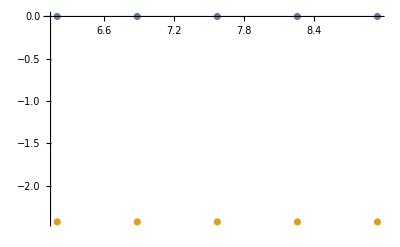

```mathematica
ListPlot[{Table[{RH[[i]],Re[Φ0RH[[i]]]},{i,1,5}],Table[{RH[[i]],Im[Φ0RH[[i]]]},{i,1,5}]}]
```

```mathematica
ClearAll[Rs]
```

```mathematica
Table[
Module[{mode},
mode = modes[[i]]
],
{i,1, Length[modes]}
]
```

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ0s= Monitor[ParallelTable[Φ0 [a , Rs[[i]] ,τmino, p,e,1],{i,1 ,Length[Rs]}],i];
]
```

```mathematica
Φ0s
```

{0.+0.0051123 ⅈ,1.26089×10^-19+0.00510965 ⅈ,1.19509×10^-19+0.00510704 ⅈ,1.13436×10^-19+0.00510445 ⅈ,1.07819×10^-19+0.00510187 ⅈ,1.02612×10^-19+0.0050993 ⅈ,0.+0.00509674 ⅈ,0.+0.00509417 ⅈ,0.+0.0050916 ⅈ,0.+0.00508902 ⅈ,3.26055×10^-19+0.00508642 ⅈ,-1.56174×10^-19+0.0050838 ⅈ,0.+0.00508117 ⅈ,0.+0.0050785 ⅈ,0.+0.00507582 ⅈ,-1.32689×10^-19+0.0050731 ⅈ,-1.27651×10^-19+0.00507035 ⅈ,0.+0.00506757 ⅈ,-1.18403×10^-19+0.00506476 ⅈ,0.+0.00506191 ⅈ,0.+0.00505902 ⅈ,-1.06316×10^-19+0.00505609 ⅈ,1.02698×10^-19+0.00505312 ⅈ,0.+0.00505011 ⅈ,-9.59977×10^-20+0.00504706 ⅈ,6.67557×10^-15+0.00793945 ⅈ,3.0531×10^-15+0.00754049 ⅈ,-1.74165×10^-15+0.0071669 ⅈ,-1.26713×10^-15+0.00681671 ⅈ,1.68898×10^-14+0.00648812 ⅈ,1.47537×10^-14+0.00617952 ⅈ,1.28385×10^-14+0.00588943 ⅈ,-2.00934×10^-15+0.00561648 ⅈ,-1.65669×10^-15+0.00535945 ⅈ,-1.36919×10^-15+0.00511719 ⅈ,-1.13221×10^-15+0.00488869 ⅈ,-9.37633×10^-16+0.00467298 ⅈ,-7.78384×10^-16+0.00446919 ⅈ,-6.48806×10^-16+0.00427653 ⅈ,-5.41056×10^-16+0.00409424 ⅈ,-1.96712×10^-15+0.00392166 ⅈ,-1.16913×10^-15+0.00375815 ⅈ,-4.79286×10^-16+0.00360312 ⅈ,1.0666×10^-16+0.00345606 ⅈ,-1.67223×10^-15+0.00331645 ⅈ,-1.4623×10^-15+0.00318384 ⅈ,2.3647×10^-16+0.0030578 ⅈ,-4.7941×10^-17+0.00293794 ⅈ,-2.33281×10^-16+0.00282388 ⅈ,-1.63305×10^-17+0.00271529 ⅈ,1.65447×10^-15+0.00261185 ⅈ,-3.74413×10^-16+0.00251326 ⅈ,-7.92624×10^-16+0.00241925 ⅈ,-6.39307×10^-16+0.00232955 ⅈ,-5.17913×10^-16+0.00224393 ⅈ,-3.3168×10^-16+0.00216217 ⅈ,-6.46811×10^-17+0.00208404 ⅈ,1.16972×10^-16+0.00200936 ⅈ,2.31069×10^-16+0.00193794 ⅈ,3.01424×10^-16+0.00186962 ⅈ,-4.73673×10^-17+0.00180421 ⅈ,-4.01952×10^-17+0.00174159 ⅈ,-3.46059×10^-17+0.00168159 ⅈ,-2.85224×10^-17+0.0016241 ⅈ,-2.35073×10^-17+0.00156898 ⅈ,-2.00468×10^-17+0.00151611 ⅈ,-1.72509×10^-17+0.00146539 ⅈ,-1.45588×10^-17+0.0014167 ⅈ,-1.15799×10^-17+0.00136996 ⅈ,-9.97307×10^-18+0.00132506 ⅈ,-8.54809×10^-18+0.00128192 ⅈ,-7.53887×10^-18+0.00124045 ⅈ,-6.32646×10^-18+0.00120058 ⅈ,-5.27401×10^-18+0.00116224 ⅈ,-4.94895×10^-18+0.00112534 ⅈ,-4.06944×10^-18+0.00108984 ⅈ,-3.77545×10^-18+0.00105565 ⅈ,-3.81842×10^-18+0.00102273 ⅈ,-2.78729×10^-18+0.000991025 ⅈ,-2.63396×10^-18+0.000960469 ⅈ,-1.86409×10^-18+0.000931019 ⅈ,-1.83255×10^-18+0.000902624 ⅈ,-2.38239×10^-17+0.000875241 ⅈ,-2.02776×10^-17+0.000848826 ⅈ,-1.73291×10^-17+0.000823338 ⅈ,-1.47601×10^-17+0.000798737 ⅈ,-1.23659×10^-17+0.000774988 ⅈ,-1.04155×10^-17+0.000752054 ⅈ,-3.96589×10^-16+0.000729903 ⅈ,3.94992×10^-17+0.000708502 ⅈ,3.47049×10^-17+0.000687821 ⅈ,3.00121×10^-17+0.000667831 ⅈ,2.661×10^-17+0.000648504 ⅈ,2.3183×10^-17+0.000629815 ⅈ,2.0394×10^-17+0.000611738 ⅈ,4.35052×10^-18+0.00059425 ⅈ,3.4442×10^-18+0.000577327 ⅈ,2.6433×10^-18+0.000560948 ⅈ,1.98231×10^-18+0.000545091 ⅈ,1.68513×10^-18+0.000529738 ⅈ,9.81249×10^-19+0.00051487 ⅈ}

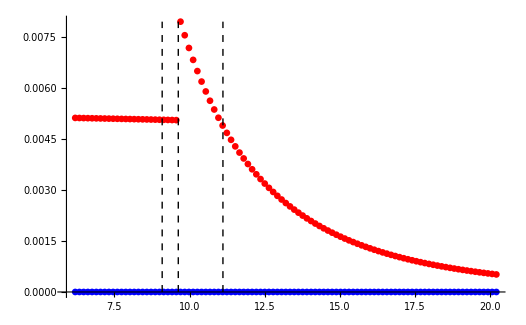

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ0s= Monitor[ParallelTable[Φ0 [a , Rs[[i]] ,τmino, p,e,2],{i,1 ,Length[Rs]}],i];
]
```

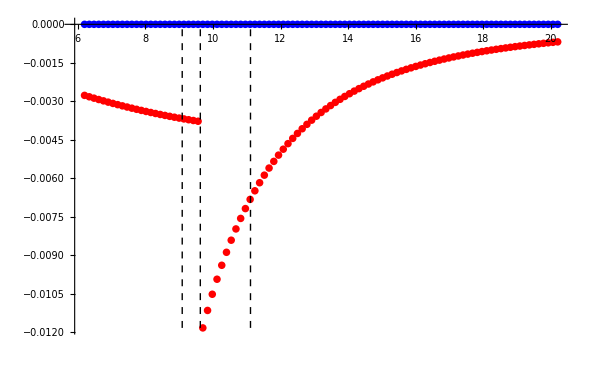

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ0s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ0s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

## Plotting Φ_2

#### Sum over l

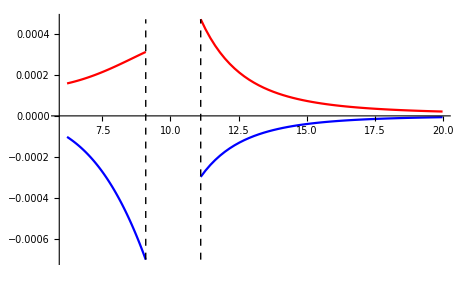

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
lowerΦ2 = Monitor[Table[Φ2 [a , lowerRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],i];
upperΦ2 =Monitor[Table[Φ2 [a , upperRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}],50+i];
]
Module[{rmax, rmin, AllData, lineStyle, line1, line2},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[lowerΦ2],Im[lowerΦ2], Re[upperΦ2],Im[upperΦ2]}];
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ2[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ2[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ2[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
]
```

Haas(2012) and  Thesis by Patrick Nolan (UCD)

### l = 1 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ2s= Monitor[ParallelTable[Φ2 [a , Rs[[i]] ,τmino, p,e,1],{i,1 ,Length[Rs]}],i];
]
```

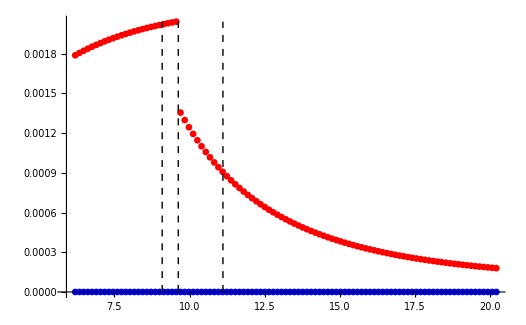

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ2s],Im[Φ2s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}
]
]
```

### l=2 mode

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
Rs = Subdivide[KerrGeoSeparatrix[a,e,1],rmin+rmax,100];
Φ2s= Monitor[ParallelTable[Φ2[a , Rs[[i]] ,τmino, p,e,2],{i,1 ,Length[Rs]}],i];
]
```

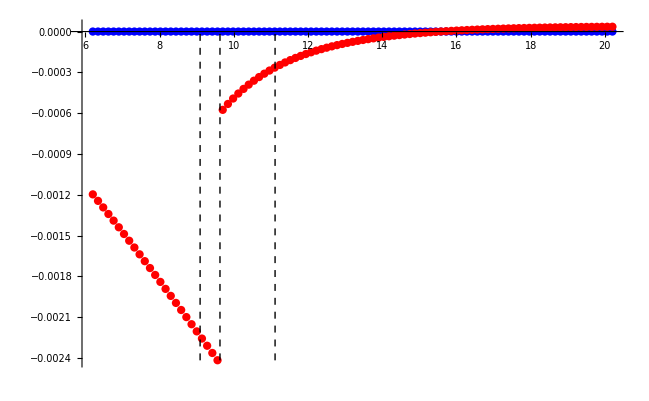

```mathematica
Module[{rmax, rmin, AllData, lineStyle, line1, line2,line3,orbit,t0,r0,θ0,ϕ0, a=0,prec=32,e=0.1,p=10,τmino=0.5},
{rmax, rmin} = OrbitTP[10,0.1];
AllData = Flatten[{Re[Φ0s],Im[Φ0s]}];
lineStyle={Thick,Black,Dashed};
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
line3= Line[{{r0[τmino],Min[AllData]},{r0[τmino],Max[AllData]}}];
ListPlot[{Table[{Rs[[i]],Re[Φ2s[[i]]]}, {i,1, Length[Rs]}] , Table[{Rs[[i]], Im[Φ2s[[i]]]},{i,1,Length[Rs]}]}, Joined->False, PlotStyle->{Blue, Red},
Epilog->{Directive[lineStyle],line1,line2,line3}, PlotRange->All
]
]
```